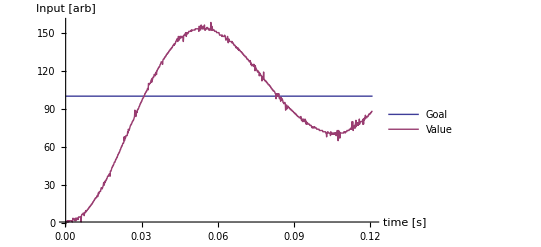

```mathematica
SetDirectory[NotebookDirectory[]];
data=Import["data.txt","Table"];
data=data[[2;;]];
goaldata=Transpose[Transpose[data][[1;;2]]];
adcdata=Transpose[{Transpose[data][[1]],Transpose[data][[3]]}];
voltage=Transpose[{Transpose[data][[1]],2*Transpose[data][[4]]}];
ListLinePlot[{goaldata[[;;1000]],adcdata[[;;1000]](*,voltage*)},PlotRange->All,PlotLegends->{"Goal","Value"},AxesLabel->{"time [s]","Input [arb]"}]
```

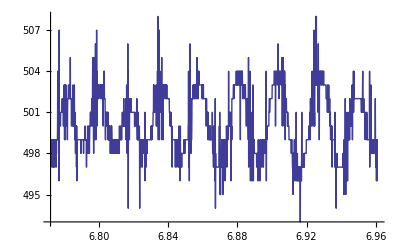

```mathematica
fitdata=adcdata[[8000;;10000]];
ListLinePlot[fitdata]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 1.87535 | 0.0566502 | 33.104 | 5.98572×10^-192
o | 500.256 | 0.0401813 | 12450. | 4.20196344736×10^-4885
p | 339.162 | 3.81788 | 88.8352 | 3.81934499167×10^-696
ω | 265.758 | 0.55586 | 478.103 | 8.03143440746×10^-2062

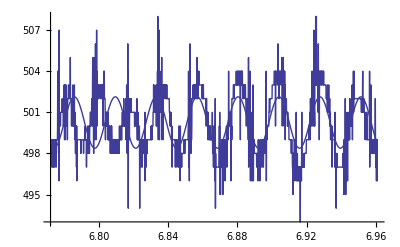

```mathematica
nlm=NonlinearModelFit[fitdata,a*Cos[t*ω+p]+o,{a,o,p,{ω,2*Pi/.02}},t];
nlm["ParameterTable"]
Show[ListLinePlot[fitdata],Plot[nlm[t],{t,fitdata[[1]][[1]],fitdata[[-1]][[1]]}]]
```